```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/lackey/Research/Poisson/Testprograms

```mathematica
Expand[1/8 ChebyshevT[4, x]-ChebyshevT[3, x]+7/2 ChebyshevT[2, x]-7ChebyshevT[1, x]+35/8 ChebyshevT[0, x]]
```

1-4 x+6 x^2-4 x^3+x^4

```mathematica
Expand[(x-1)^4]
```

1-4 x+6 x^2-4 x^3+x^4

```mathematica
Expand[-1/160 ChebyshevT[4, x]+7/120 ChebyshevT[2, x]-329/480 ChebyshevT[0, x]]
```

-3/4+x^2/6-x^4/20

```mathematica
Expand[-0.1*ChebyshevT[2, x]-1.6*ChebyshevT[1, x]+1.7*ChebyshevT[0, x]]
```

1.8-1.6 x-0.2 x^2

```mathematica
R=5;
α=1;
β=4;
N[Expand[R-(α*x+β)^2/R]]
```

1.8-1.6 x-0.2 x^2

## (spherically symmetric source, not compact)

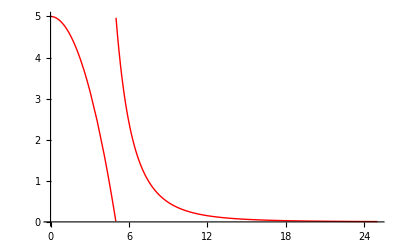

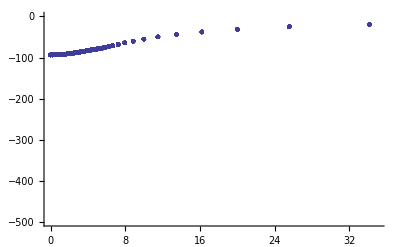

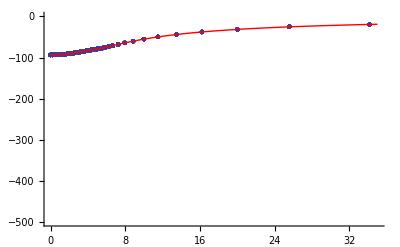

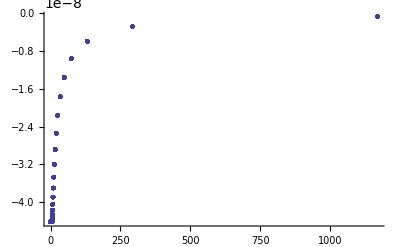

```mathematica
R=5;
sin[r_]:=R-r^2/R;
sout[r_]:=R^5/r^4;
s[r_]:=Piecewise[{{sin[r], r<R}, {sout[r], r≥R}}]
fin[r_]:=(R*r^2)/6-r^4/(20R)-(3 R^3)/4;
fout[r_]:=R^5/(2 r^2)-(17 R^4)/(15r);
f[r_]:=Piecewise[{{fin[r], r<R}, {fout[r], r≥R}}]
Plot[s[r], {r, 0, 5*R}, PlotStyle->Red]
fofrtpdata=Import["fofrtp.txt", "Data"];
rmax=(*fofrtpdata⟦-1,1⟧*)35;
plot1=ListPlot[fofrtpdata⟦All, {1, 4}⟧, PlotRange->{{0, rmax},{-500, 0}}]
plot2=Plot[f[r], {r, 0, 35}, PlotRange->{{0, rmax},{-100, 0}}, PlotStyle->Red];
Show[plot1, plot2]
ListPlot[Table[{fofrtpdata⟦i, 1⟧, fofrtpdata⟦i, 4⟧-f[fofrtpdata⟦i, 1⟧]}, {i, Length[fofrtpdata]}](*, PlotRange->{All, {0, 1*^-11}}*)]
```

## (not spherically symmetric, compact)

```mathematica
R=5.0;
L=5;
sin[r_, θ_, ϕ_]:=SphericalHarmonicY[L, 0, θ, ϕ] 1/2(L+3)(L+5)((L-4)r^2/R^(L+5)-(L-2)1/R^(L+3));
s[r_, θ_, ϕ_]:=Piecewise[{{sin[r, θ, ϕ], r<R}, {0, r≥R}}]
fin[r_, θ_, ϕ_]:=SphericalHarmonicY[L, 0, θ, ϕ]((L+5)r^2/(2*R^(L+3))-(L+3)r^4/(2*R^(L+5)));
fout[r_, θ_, ϕ_]:=SphericalHarmonicY[L, 0, θ, ϕ] 1/r^(L+1);
f[r_, θ_, ϕ_]:=Piecewise[{{fin[r, θ, ϕ], r<R}, {fout[r, θ, ϕ], r≥R}}]
```

```mathematica
rofxy[x_, y_]:=√(x^2+y^2)
θofxy[x_, y_]:=Piecewise[{{ArcTan[y/x], x<0}, {π+ArcTan[y/x], x>0}, {0, x=0}}]
```

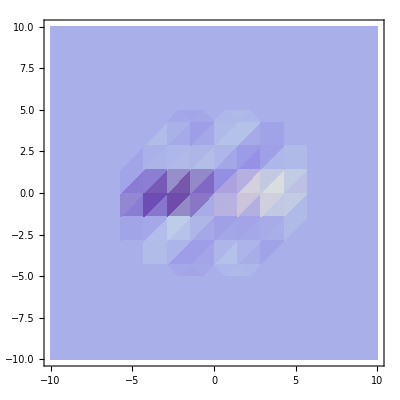

```mathematica
DensityPlot[s[rofxy[x, y], θofxy[x, y], 0],{x,-10,10},{y,-10,10}]
```

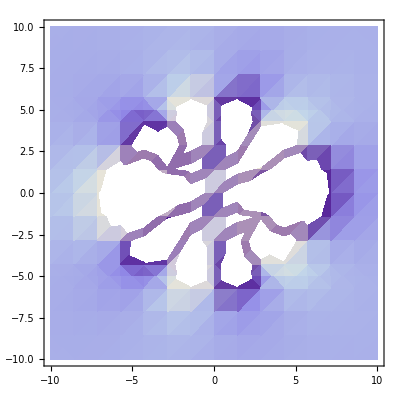

```mathematica
DensityPlot[f[rofxy[x, y], θofxy[x, y], 0],{x,-10,10},{y,-10,10}]
```

```mathematica
nz=5;
nr=25;
np=12;
nt=np/2 + 1
```

7

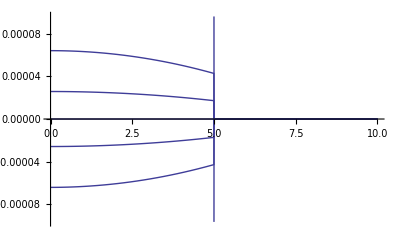

```mathematica
Plot[Table[s[r, N[(π*j)/(nt-1)], 0], {j, 0, nt-1}], {r, 0, 10}(*, PlotRange->All*)]
```

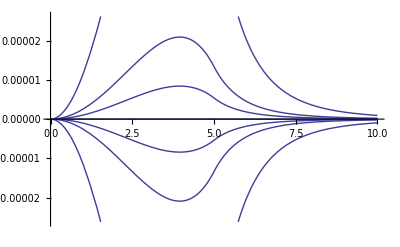

```mathematica
plot1=Plot[Table[f[r, N[(π*j)/(nt-1)], 0], {j, 0, nt-1}], {r, 0, 10}(*, PlotRange->All*)]
```

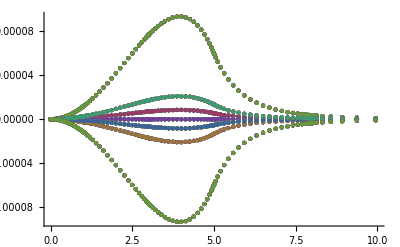

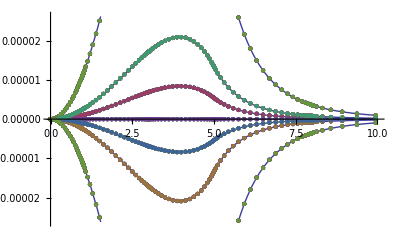

```mathematica
fofrtpdata=Partition[Partition[Import["fofrtp.txt", "Data"],np], nt];
plot2=ListPlot[Flatten[Table[fofrtpdata⟦All, j, k, {1, 4}⟧, {j, 1, nt} , {k, 1, np}], 1], PlotRange->{{0, 10}, All}]
Show[plot1, plot2]
```

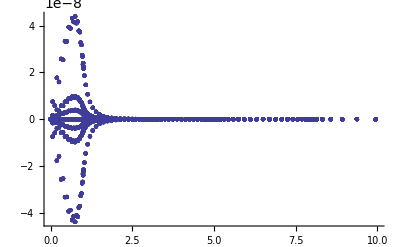

```mathematica
fofrtpdataflat=Import["fofrtp.txt", "Data"];
ListPlot[Table[{fofrtpdataflat⟦i, 1⟧, fofrtpdataflat⟦i, 4⟧-f[fofrtpdataflat⟦i, 1⟧, fofrtpdataflat⟦i, 2⟧, fofrtpdataflat⟦i, 3⟧]}, {i, Length[fofrtpdataflat]}], PlotRange->{{0, 10}, All}]
```

## (not spherically symmetric, compact, valid for even AND odd L)

```mathematica
(*R=5.0;
L=5;*)
sin[r_]:=r^L((2L+3)(2L+5)1/R^(2L+3)-(4L+10)(2L+3)r^2/R^(2L+5));
s[r_, θ_, ϕ_]:=Piecewise[{{sin[r]SphericalHarmonicY[L, 0, θ, ϕ], r<R}, {0, r≥R}}]
fin[r_]:=r^L(1/2(2L+5)r^2/R^(2L+3)-1/2(2L+3)r^4/R^(2L+5));
fout[r_]:=1/r^(L+1);
f[r_, θ_, ϕ_]:=Piecewise[{{fin[r]SphericalHarmonicY[L, 0, θ, ϕ], r<R}, {fout[r]SphericalHarmonicY[L, 0, θ, ϕ], r≥R}}]
```

```mathematica
Simplify[fin''[r]+2/r fin'[r]-(L(L+1))/r^2 fin[r]-sin[r]]
```

0

```mathematica
Simplify[sin[r]]
```

2 r^L R^(-5-2 L) (-(5+L) (3+2 L) r^2+(1+L) (5+2 L) R^2)

```mathematica
sin[r_]:=r^L(a+b r^2);
fin[r_]:=r^L(c r^2+d r^4);
fout[r_]:=1/r^(L+1);
```

```mathematica
lapfin[r_]:=Simplify[fin''[r]+2/r fin'[r]-(L(L+1))/r^2 fin[r]]
```

```mathematica
fin[R]-fout[R]
```

-R^(-1-L)+R^L (c R^2+d R^4)

```mathematica
fin'[R]-fout'[R]
```

-(-1-L) R^(-2-L)+R^L (2 c R+4 d R^3)+L R^(-1+L) (c R^2+d R^4)

```mathematica
Solve[{fin[R]-fout[R]==0,fin'[R]-fout'[R]==0},{c,d}]
```

{{c→1/2 (5+2 L) R^(-3-2 L),d→-1/2 (3+2 L) R^(-5-2 L)}}

```mathematica
lapfin[r]
```

2 r^L (c (3+2 L)+2 d (5+2 L) r^2)

## non-rotating n=1 polytrope

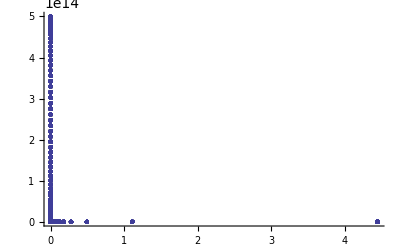

```mathematica
rhoofrtpdata=Import["rhoofrtp.txt", "Data"];
plot1=ListPlot[rhoofrtpdata⟦All, {1, 4}⟧]
```

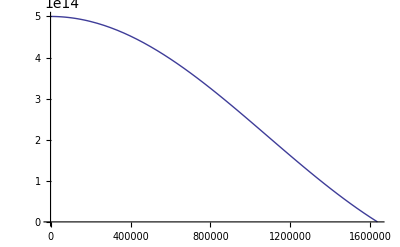

```mathematica
plot2=Plot[5*^14*Sin[π*x/1.6354*^6]/(π*x/1.6354*^6), {x, 0, 1.6354*^6}]
```

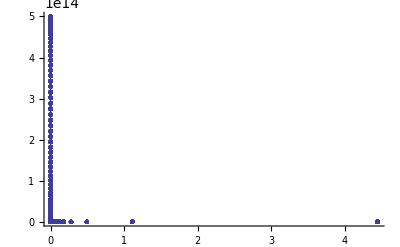

```mathematica
Show[plot1, plot2]
```